Okeefe Niemann
6/1/2014
1281465
PHYS 115

## Assignment 8

### Question 1

Part a, b, c, e, f, g:

See handwritten page on back of assignment.

Part d :

```mathematica
clear["Global`*"];
```

```mathematica
mandelbrot[cx_, cy_, lim_] := Module[{z=0, ct=0}, While[Abs[z]<2.0&&ct≤lim, z=z^2+cx+I cy;++ct];-ct];
```

```mathematica
mandelbrotc = Compile[{cx,cy,lim}, mandelbrot[cx, cy, lim]];
```

```mathematica
DensityPlot[-mandelbrotc[x,y,200],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->200,Mesh->False,ColorFunction->(Hue[0.75#1^0.6]&), FrameLabel -> {"c_x", "c_y"}]
```

-Graphics-

### Question 2

Part a :

```mathematica
r:= 26.5
σ:= 10
b:=8/3
```

```mathematica
lorenzeq:=NDSolve[{x'[t]==-σ x[t]+σ y[t], y'[t]== -x[t] z[t] + r x[t] - y[t], z'[t]== x[t] y[t]-b z[t], x[0]==1, y[0]==0, z[0]==0}, {x,y,z},{t,150}, MaxSteps->200000]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.lorenzeq],{t,0,110}, AxesLabel->{"x","y","z"} ,ColorFunction->"NeonColors"]
```

-Graphics3D-

Part b:

```mathematica
Evaluate[{x[t],y[t],z[t]}/.lorenzeq]
```

{{InterpolatingFunction[{{0.,80.}},<>][t],InterpolatingFunction[{{0.,80.}},<>][t],InterpolatingFunction[{{0.,80.}},<>][t]}}

```mathematica
x[3]/.lorenzeq
```

{-9.36835}

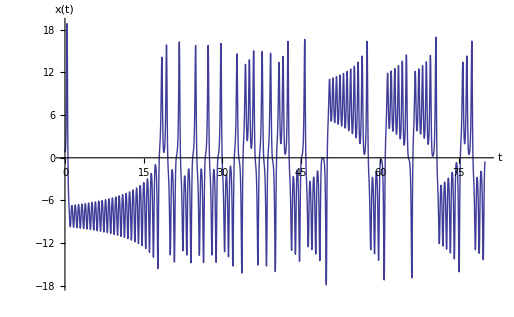

```mathematica
Plot[Evaluate[{x[t]}/.lorenzeq],{t,0,80},PlotRange->All, AxesLabel->{"t", "x(t)"}]
```

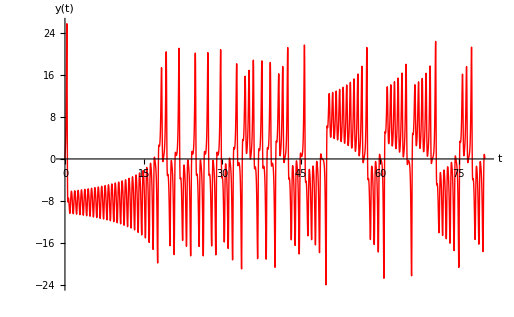

```mathematica
Plot[Evaluate[{y[t]}/.lorenzeq],{t,0,80},PlotRange->All, AxesLabel->{"t", "y(t)"}, PlotStyle->Red]
```

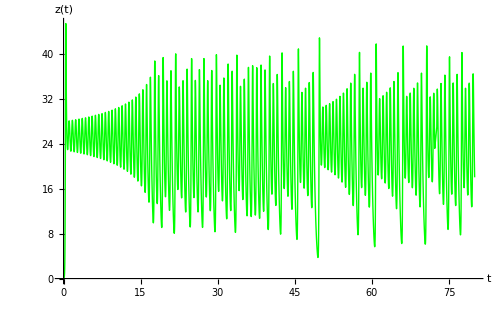

```mathematica
Plot[Evaluate[{z[t]}/.lorenzeq],{t,0,80},PlotRange->All, AxesLabel->{"t", "z(t)"}, PlotStyle->Green]
```

While there does seem to be some form of structure for all axes, this system never settles into a limit cycle of any order and thus is chaotic. These structures are called “strange attractors”, and give the system a pattern-like appearance even though fixed points vary throughout the volume. This specific ratio of parameters is called the “Lorenz attractor,” and was the first of these strange attractors to be discovered.

### Question 3

Part a:

```mathematica
Clear["Global`*"];
```

```mathematica
a=0.200005; f=0.52; Ω=0.694001;cycles= 50;
```

```mathematica
sol3=NDSolve[{θ'[t]==ω[t],ω'[t]==-Sin[θ[t]]-a ω[t]+f Cos[Ω t], θ[0]==0.8,ω[0]==0.8},{θ,ω},{t,0,cycles (2 Pi / Ω)},MaxSteps->20000];
reduce[θ_]:=Mod[θ,2 Pi]/;Mod[θ,2 Pi]≤Pi;
reduce[θ_]:=(Mod[θ,2 Pi]-2 Pi)/;Mod[θ,2 Pi]>Pi;
steps=30;
points3=Flatten[Table[{θ[t],ω[t]}/.sol3,{t,0,cycles(2 Pi/Ω),(1/steps)(2 Pi/Ω)}],1];
newpoints3={reduce[#[[1]]],#[[2]]}&/@points3;
```

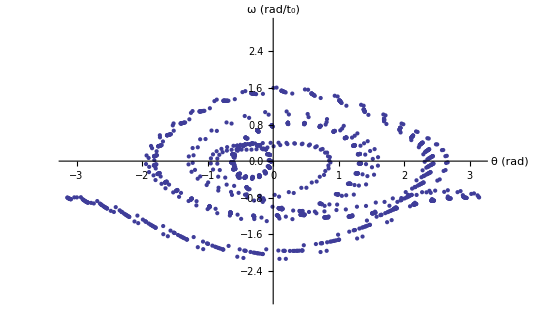

```mathematica
ListPlot[newpoints3,PlotRange->{-3,3},AxesLabel->{"θ (rad)","ω (rad/t_0)"}]
```

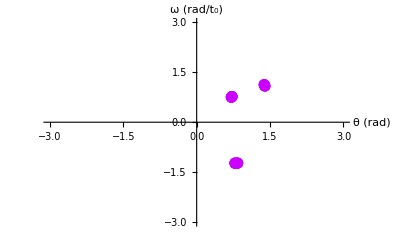

```mathematica
poincare=Table[newpoints3[[n]],{n,1+25 steps,Length[newpoints3],steps}];
ListPlot[poincare,PlotRange->{{-3,3},{-3,3}},PlotStyle->{Hue[.8],PointSize[0.02]},AxesLabel->{"θ (rad)","ω (rad/t_0)"}]
```

As shown by the above poincare section, the motion resulting from the inputted parameters displays a periodic motion with 3-4 fixed points (though it could be as great as 6 given relatively low resolution of the graph).

Part b:

```mathematica
Clear["Global`*"];
```

```mathematica
a=1/2; f=1.15;Ω=2/3; cycles=180;
```

```mathematica
sol4=NDSolve[{θ'[t]==ω[t],ω'[t]==-Sin[θ[t]]-a ω[t]+f Cos[Ω t], θ[0]==0.8,ω[0]==0.8},{θ,ω},{t,0,cycles (2 Pi / Ω)},MaxSteps->500000];
reduce[θ_]:=Mod[θ,2 Pi]/;Mod[θ,2 Pi]≤Pi;
reduce[θ_]:=(Mod[θ,2 Pi]-2 Pi)/;Mod[θ,2 Pi]>Pi;
```

```mathematica
steps=100;
```

```mathematica
points4=Flatten[Table[{θ[t],ω[t]}/.sol4,{t,0,cycles(2 Pi/Ω),(1/steps)(2 Pi/Ω)}],1];
```

```mathematica
newpoints4={reduce[#[[1]]],#[[2]]}&/@points4;
```

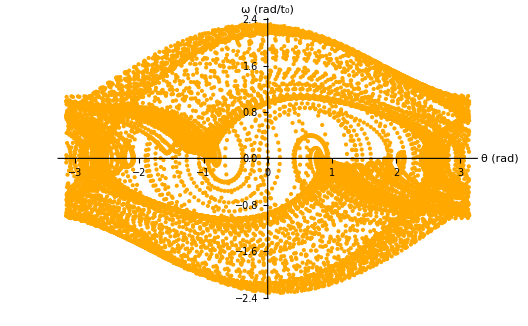

```mathematica
ListPlot[newpoints4,AxesLabel->{"θ (rad)","ω (rad/t_0)"}, PlotStyle->{Hue[0.11]}]
```

```mathematica
poincare1= Table[newpoints4[[n]],{n,1+25 steps,Length[newpoints4],steps}];
```

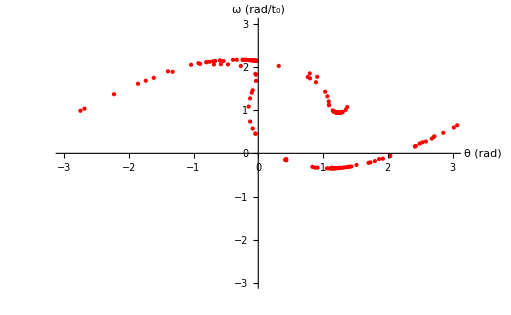

```mathematica
ListPlot[poincare1,PlotRange->{{-3,3},{-3,3}}, PlotStyle->{Hue[0]},AxesLabel->{"θ (rad)","ω (rad/t_0)"}]
```

As shown above, the system is chaotic, though it doesn't appear "random" by any means.

### Question 4

Part a, b:

See handwritten page on back of assignment.

Part c:

```mathematica
l0:=1
```

```mathematica
l[n_]:= (4/3)^n
```

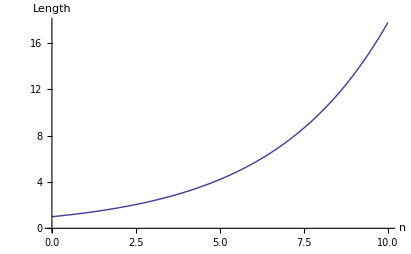

```mathematica
Plot[l[n],{n,0,10}, AxesLabel->{"n","Length"}]
```

The above graph shows that, though the lines become increasingly short, the iterations increases their abuncdancy to a greater  degree. Thus, after infinite iterations, the length of the curve will approach infinity

Part D :

```mathematica
Clear["Global`*"]
```

```mathematica
rotate90[{x_,y_}]:={-y,x}
```

```mathematica
koch[p1_,p2_,n_]:={koch[p1,p1+(p2-p1)/3,n-1],koch[p1+(p2-p1)/3,(p1+p2)/2+Sqrt[3]/6 rotate90[p2-p1],n-1],koch[(p1+p2)/2+Sqrt[3]/6 rotate90[p2-p1],p2-(p2-p1)/3,n-1],koch[p2-(p2-p1)/3,p2,n-1]}
```

```mathematica
koch[p1_,p2_,0]:=Line[{p1,p2}]
```

```mathematica
snowflake[n_]:=Graphics[{koch[{0,0},{1,0},n],koch[{1,0},{1/2,-Sqrt[3]/2},n],koch[{1/2,-Sqrt[3]/2},{0,0},n]}]
```

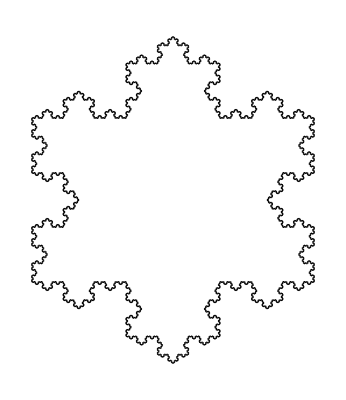

```mathematica
snowflake[5]
```

### Question 5

Part a:

```mathematica
V0:=25; L:=1;
```

```mathematica
V[x_]:= -V0/2 (1+Cos[2Pi x/L])
```

```mathematica
piecewise:=Piecewise[{{V[x],-L/2<x<L/2},{0,-L/2>x>L/2}}]
```

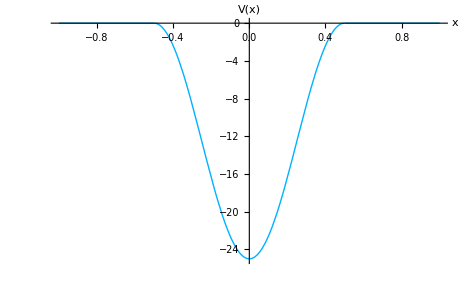

```mathematica
Plot[piecewise,{x,-L,L}, AxesLabel->{"x","V(x)"}, PlotStyle->{Hue[.55]}]
```

Part b :

In the regions to the left/right of the potential well, the wave function will experience and exponential decay. By generally defining our wave functions and solving for boundary conditions, I will be able to determine the energy of the ground state.

```mathematica
Clear["Global`*"]
```

```mathematica
B=1; V0=25; L=1;
```

```mathematica
v[x_]:=-V0/2 (1+Cos[2Pi x/L])/;Abs[x]≤L/2
v[x_]:=0/;Abs[x]>L/2
```

```mathematica
ψl[x_]:=A Exp[Abs[2 en]^(1/2) x]
ψr[x_]:=B Exp[-Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_]:=ψwell''[x]+2(en-v[x])ψwell[x]
```

```mathematica
wavefuncwell[energy_]:=(en=energy;NDSolve[{eqn[energy]==0,ψwell[-L/2]==ψl[-L/2],ψwell'[-L/2]==ψl'[-L/2]},ψwell,{x,-L/2,0}])
```

```mathematica
solwell[x_?NumericQ,en_?NumericQ]:=ψwell[x]/.wavefuncwell[en][[1]]
```

```mathematica
solwellprime[x_?NumericQ,en_?NumericQ]:=ψwell'[x]/.wavefuncwell[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval=energy/. FindRoot[solwellprime[0,energy],{energy,-10,-5}]
```

-15.329

As calculated above, E= -15.329.

```mathematica
efuncwell[x_]=ψwell[x]/.wavefuncwell[eval][[1]];
```

```mathematica
ψun[x_]:=efuncwell[-x]/;0≤x≤L/2
ψun[x_]:=efuncwell[x]/;-L/2≤x<0
ψun[x_]:=ψl[x]/;x<-L/2
ψun[x_]:=ψr[x]/;x>L/2
```

```mathematica
norm = Sqrt[NIntegrate[ψun[x]^2,{x,-Infinity,Infinity}]];
```

```mathematica
ψ[x_]:=ψun[x]/norm;
```

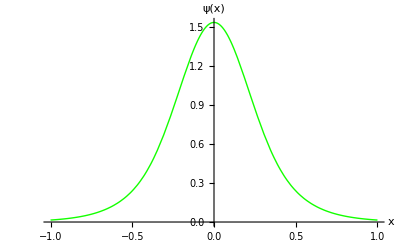

```mathematica
Plot[ψ[x],{x,-1,1},AxesLabel->{"x","ψ(x)"},PlotStyle->{Hue[.32]}]
```

Part c:

```mathematica
A=-B;
```

```mathematica
Plot[solwell[0,en],{en,-5,5}]
```

```mathematica
eval=en/.FindRoot[solwell[0,en],{en,-2,0}]
```

-0.92539

As calculated above, E = -.92539.

```mathematica
efuncwell[x_]=ψwell[x]/.wavefuncwell[eval][[1]];
```

```mathematica
ψun[x_]:=-efuncwell[-x]/;0≤x≤L/2
```

```mathematica
norm=Sqrt[NIntegrate[ψun[x]^2,{x,-Infinity,Infinity}]];
```

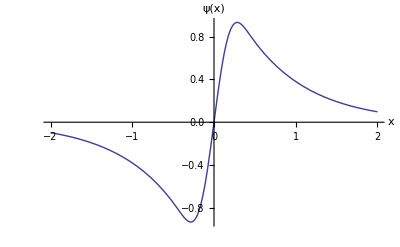

```mathematica
Plot[ψ[x],{x,-2,2}, AxesLabel->{"x","ψ(x)"}]
```

### Question 6

Part a :

```mathematica
Clear["Global`*"]
```

```mathematica
L=10;
```

```mathematica
v[x_]:=-Sech[x]^2/;Abs[x]≤L/2
```

```mathematica
v[x_]:=0/;Abs[x]>L/2
```

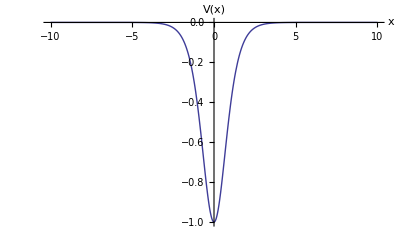

```mathematica
Plot[v[x],{x,-10,10},PlotRange->All, AxesLabel->{"x","V(x)"}]
```

Part b :

```mathematica
B=1;
```

```mathematica
ψl[x_]:=A Exp[Abs[2 en]^(1/2) x]
```

```mathematica
ψr[x_]:=B Exp[-Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_]:=ψwell''[x]+2(en-v[x])ψwell[x]
```

```mathematica
wavefuncwell[energy_]:=(en=energy;NDSolve[{eqn[energy]==0,ψwell[-L/2]==ψl[-L/2],ψwell'[-L/2]==ψl'[-L/2]},ψwell,{x,-L/2,0}])
```

```mathematica
solwell[x_?NumericQ,en_?NumericQ]:=ψwell[x]/. wavefuncwell[en][[1]]
```

```mathematica
solwellprime[x_?NumericQ,en_?NumericQ]:=ψwell'[x]/. wavefuncwell[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval=energy/. FindRoot[solwellprime[0,energy],{energy,-1,0}]
```

-0.5

```mathematica
efuncwell[x_]=ψwell[x]/.wavefuncwell[eval][[1]];
```

```mathematica
ψ[x_]:=efuncwell[x] /;-L/2≤x≤0
ψ[x_]:=efuncwell[-x] /;0≤x≤L/2
ψ[x_]:=ψl[x] /;x<-L/2
ψ[x_]:=ψr[x] /;x>L/2
```

```mathematica
norm=Sqrt[NIntegrate[ψ[x]^2,{x,-Infinity,Infinity}]];
```

```mathematica
ψnorm[x_]=ψ[x]/norm
```

0.707107 Sech[x]

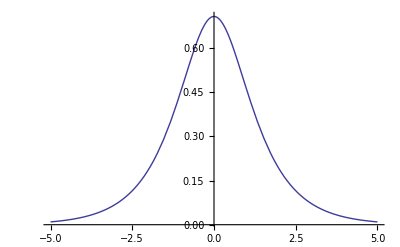

```mathematica
Plot[ψnorm[x],{x,-.5L,.5L},PlotRange->All]
```

Part c :

```mathematica
Clear["Global`*"]
```

```mathematica
ψ[x_]=1/Sqrt[2] Sech[x];
V[x_]=-Sech[x]^2;
```

```mathematica
D[Sech[x]/(√2), x]//TrigReduce;
```

```mathematica
∂_x %;
```

```mathematica
ψnew[x_]=%;
```

```mathematica
energy[x_]=Solve[ψnew[x]+2(y-V[x])ψ[x]==0,y];
```

```mathematica
y/.energy[0][[1]]
```

-1/2

Compared to the wave function and eigenvalue of part two, the exact values of the two correspond perfectly with the approximation of the potential at |x| = 5. This shows that the tails of the wave function contribute a negligible amount to the normalizing constant of the wave function, as well as to the energy eigenvalue.